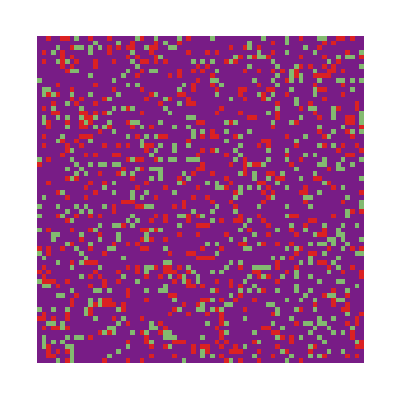

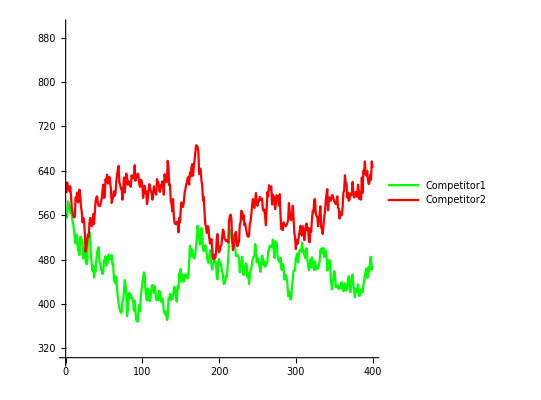

```mathematica
iran=70;
jran=70;
gen=400;
ArrayPlot[field=Table[RandomChoice[{1,-1,-1,-1,-1,-1,-1,0}],{i,1,iran},{j,1,jran}],ColorFunction->"Rainbow"]
field1=field;
list1={};
list2={};
Do[
{Do[
Do[{
If[field[[i]][[j]]==1,{field1[[i]][[j]]=RandomChoice[{-1,1}],field1[[i+RandomChoice[{-1,0,1}]]][[j+RandomChoice[{-1,0,1}]]]=RandomChoice[{1,1,1,-1}]}],
If[field[[i]][[j]]==0,{field1[[i]][[j]]=RandomChoice[{-1,0}],field1[[i+RandomChoice[{-1,0,1}]]][[j+RandomChoice[{-1,0,1}]]]=RandomChoice[{0,0,0,-1}]}]
},{j,2,jran-1}],{i,2,iran-1}],
AppendTo[list1,Count[Flatten[field],0]],
AppendTo[list2,Count[Flatten[field],1]]
,field=field1,Subscript[p1, k]=ArrayPlot[field1,ColorFunction->"Rainbow",PlotLabel->"Generation="<>ToString[k]],
Subscript[p2, k]=ListPlot[{list1,list2},AspectRatio->1,PlotRange->{Automatic,{300,900}},PlotStyle->{Green,Red},AxesLabel->{"time","population"},PlotLegends->{"Competitor1","Competitor2"},Joined->True]}
,{k,1,gen}]
ListPlot[{list1,list2},AspectRatio->1,PlotRange->{Automatic,{300,900}},PlotStyle->{Green,Red},PlotLegends->{"Competitor1","Competitor2"},Joined->True]
gif1=Table[Subscript[p1, k],{k,1,gen}];
gif2=Table[Subscript[p2, k],{k,1,gen}];
Export["E:\\test_gif(1).gif",gif1];
Export["E:\\test_gif(2).gif",gif2];
SystemOpen["E:\\test_gif(1).gif"];
SystemOpen["E:\\test_gif(2).gif"];
```